```mathematica
Clear[P,ρ,K]
```

```mathematica
ρ[r_]:=Subscript[ρ, 0]*(1-r^2/L^2)
```

```mathematica
P[r_]:=1/3*(ρ[r]-K)
```

```mathematica
ρ[r]
```

(1-r^2/L^2) ρ_0

```mathematica
P[r]
```

1/3 (-K+(1-r^2/L^2) ρ_0)

```mathematica
PSubstituted[r_]:=P[r]/. {K->225,L->16,Subscript[ρ, 0]->450}
```

```mathematica
Equation1=PSubstituted[r]==0
```

1/3 (-225+450 (1-r^2/256))==0

```mathematica
Solve[Equation1,r]
```

{{r→-8 √2},{r→8 √2}}

```mathematica
N[8√2]
```

11.3137

```mathematica
P[r]
```

1/3 (-K+(1-r^2/L^2) ρ_0)

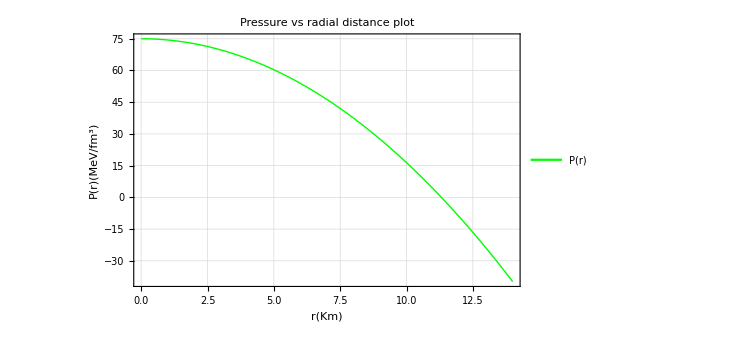

```mathematica
(*Plot P[r] vs.r with frame and legend*)Plot[PSubstituted[r],{r,0,14},PlotStyle->{Thick,Green},PlotLegends->Placed[LineLegend[{"P(r)"},LegendLayout->"Column",LegendFunction->"Panel"],{0.80,0.1}],Frame->True,FrameStyle->Directive[Brown,Thick],FrameLabel->{Style["r(Km)",Bold,15,Black],Style["P(r)(MeV/fm^3)",Bold,15,Black]},PlotLabel->Style["Pressure vs radial distance plot",Bold,20,Red],LabelStyle->Directive[Bold,Black,15],GridLines->Automatic,ImageSize->{550,350}]
```

```mathematica
ρ[r]
```

(1-r^2/L^2) ρ_0

```mathematica
ρSubstituted[r_]:=ρ[r]/.{L->16,Subscript[ρ, 0]->450}
```

```mathematica
ρSubstituted[r]
```

450 (1-r^2/256)

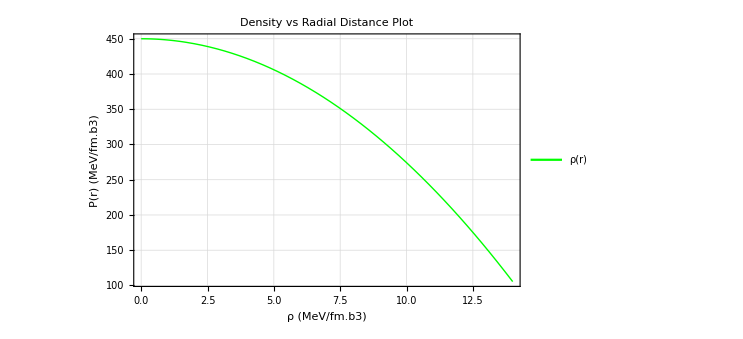

```mathematica
Plot[ρSubstituted[r],{r,0,14},PlotStyle->{Thick,Green},PlotLegends->Placed[LineLegend[{"ρ(r)"},LegendLayout->"Column",LegendFunction->"Panel"],{0.80,0.1}],Frame->True,FrameStyle->Directive[Brown,Thick],FrameLabel->{Row[{Style["ρ",Bold,15,Black],Style[" (MeV/fm.b3)",Bold,15,Black]},Spacings->{1}],Row[{Style["P(r)",Bold,15,Black],Style[" (MeV/fm.b3)",Bold,15,Black]},Spacings->{1}]},PlotLabel->Style[Column[{"Density vs Radial Distance Plot",Spacer[10] (*Adjust the number to control the vertical gap*)}],Bold,18,Red],LabelStyle->Directive[Bold,Black,15],GridLines->Automatic,ImageSize->{550,350}]
```

```mathematica
ρ1[r_]:=ρ[r]/.{Subscript[ρ, 0]->450,L->16}
```

```mathematica
ρ1[r]
```

450 (1-r^2/256)

```mathematica
P1[r_]:=1/3*(ρ1[r]-K)/.{K->225}
```

```mathematica
P1[r]
```

1/3 (-225+450 (1-r^2/256))

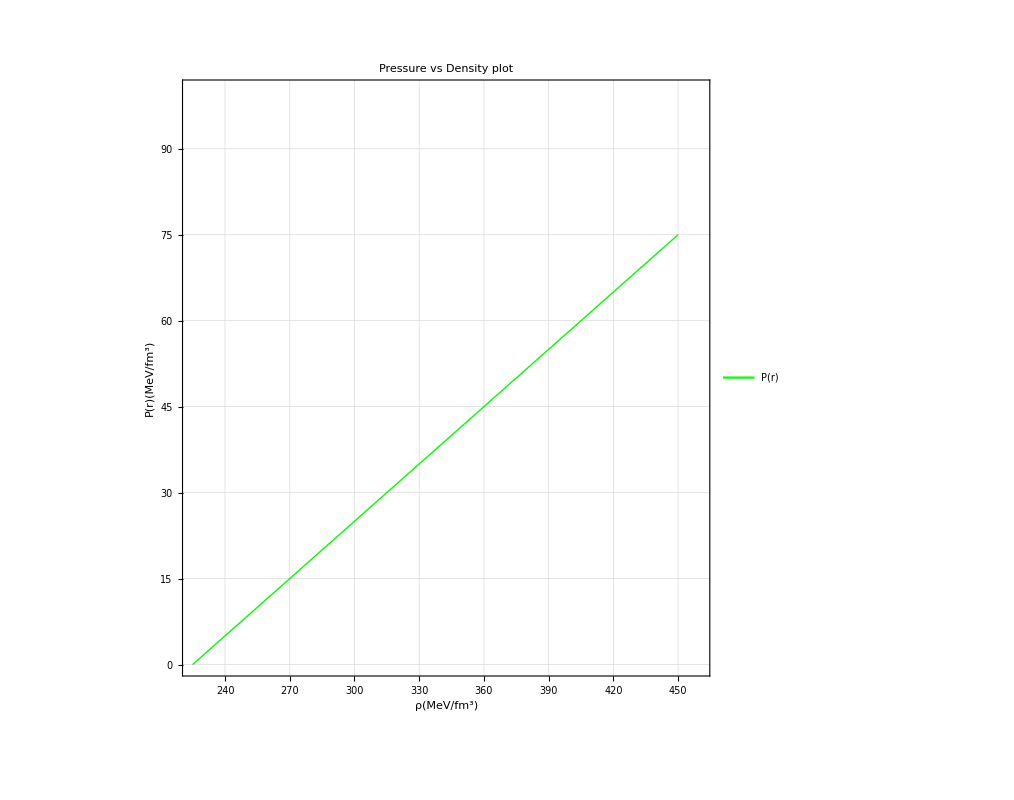

```mathematica
ParametricPlot[{ρ1[r],P1[r]},{r,0,11.3137},PlotStyle->{Thick,Green},PlotLegends->Placed[LineLegend[{"P(r)"},LegendLayout->"Column",LegendFunction->"Panel",LabelStyle->{Bold,20}],{0.80,0.1}],Frame->True,FrameStyle->Directive[Brown,Thick],FrameLabel->{Style["ρ(MeV/fm^3)",Bold,15,Black],Style["P(r)(MeV/fm^3)",Bold,15,Black]},PlotLabel->Style["Pressure vs Density plot",Bold,20,Red],LabelStyle->Directive[Bold,Black,15],GridLines->Automatic,ImageSize->{750,800},FrameTicks->{(*Bottom ticks*){{225,250,300,350,400,450},None},(*Left ticks*){{0,10,20,30,40,50,60},None},(*Top ticks*){{225,250,300,350,400,450},None},(*Right ticks*){{0,10,20,30,40,50,60},None}},FrameTicksStyle->{Directive[Blue,17],(*Bottom ticks*)Directive[Red,17],(*Left ticks*)Directive[Brown,17],(*Top ticks*)Directive[Black,17]},PlotRange->{{225,460},{0,100}}]
```